This is channel functions from datasheet: https://cdn.sparkfun.com/assets/0/8/e/2/3/AS7341_DS000504_3-00.pdf

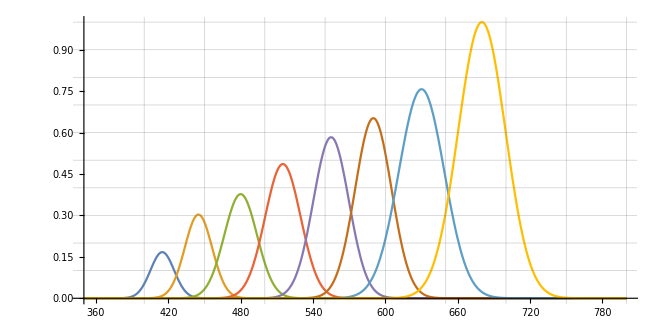

```mathematica
f[x_,mu_,range_,rel_]:=Module[{sig},
sig=-(range^2)/Log[0.03];
Exp[-(x-mu)^2/sig]*rel]
f415[x_]:=f[x,415,26,0.167];
f445[x_]:=f[x,445,30,0.303];
f480[x_]:=f[x,480,36,0.377];
f515[x_]:=f[x,515,39,0.486];
f555[x_]:=f[x,555,39,0.583];
f590[x_]:=f[x,590,40,0.652];
f630[x_]:=f[x,630,50,0.757];
f680[x_]:=f[x,680,52,1];
Exp[-((x-mu)^2)/(2*sig^2)];
Plot[{f415[x], f445[x], f480[x], f515[x], f555[x], f590[x], f630[x], f680[x]}
,{x,350,800},PlotRange->{0,1 },AspectRatio->1/2,GridLines->{Range[350,800,50], Range[0,1,0.1]}]
```

Utilitary function to print result c++ functions

```mathematica
printChanelCodeFunc[fit_]:=StringRiffle[Table[ToString[r[[2]],InputForm]<>"f * ch"<>SymbolName[r[[1]]],{r,fit}]," + "];
```

Raw set of prints from Fuji Crystal Spectral Dye density curves: https://asset.fujifilm.com/www/us/files/2020-02/04d1bef46c15a1881cb15f3e3a9f46d1/Fujicolor_Crystal_Archive_Paper_Pearl.pdf

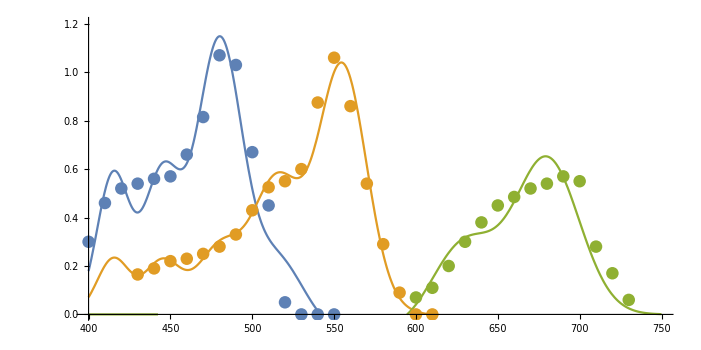

```mathematica
bluePoints={{400,0.3},{410,0.46},{420,0.52},{430,0.54},{440,0.56},{450,0.57},{460,0.66},{470,0.815},{480,1.07},{490,1.03},{500,0.67},{510,0.45},{520,0.05},{530,0},{540,0},{550,0}};

greenPoints={{430,0.165},{440,0.19},{450,0.22},{460,0.23},{470,0.25},{480,0.28},{490,0.33},{500,0.43},{510,0.525},{520,0.55},{530,0.6},{540,0.875},{550,1.06},{560,0.86},{570,0.54},{580,0.29},{590,0.09},{600,0},{610,0}};

redPoints={{600,0.07},{610,0.11},{620,0.2},{630,0.3},{640,0.38},{650,0.45},{660,0.485},{670,0.52},{680,0.54},{690,0.57},{700,0.55},{710,0.28},{720,0.17},{730,0.06}};


blueModelFunction=K415*f415[x]+K445*f445[x]+K480*f480[x]+K515*f515[x]+K555*f555[x];
greenModelFunction=K415*f415[x]+K445*f445[x]+K480*f480[x]+K515*f515[x]+K555*f555[x]+K590*f590[x]+K630*f630[x];
redModelFunction=K590*f590[x]+K630*f630[x]+K680*f680[x];


blueFit=FindFit[bluePoints,blueModelFunction,     {K415,K445,K480,K515,K555},x];
greenFit = FindFit[greenPoints,greenModelFunction,{K415,K445,K480,K515,K555,K590,K630},x];
redFit=FindFit[redPoints,redModelFunction,           {K590,K630,K680},x];

blue=blueModelFunction/. blueFit;
green=greenModelFunction/. greenFit;
red=redModelFunction/. redFit;

Show[
Plot[{blue,green,red},{x,400,750},PlotRange->{0,1.202},AspectRatio->1/2, GridLines->{xGridLine, yGridLine}],
ListPlot[{bluePoints,greenPoints, redPoints}]
]
```

```mathematica
printChanelCodeFunc[SortBy[redFit,First]]
printChanelCodeFunc[SortBy[greenFit,First]]
printChanelCodeFunc[SortBy[blueFit,First]]
```

-0.0812698108293189f * chK590 + 0.3889645588671796f * chK630 + 0.6435851049073148f * chK680

1.3625505596392686f * chK415 + 0.7230896797200832f * chK445 + 0.7186750494198619f * chK480 + 1.1292803233662263f * chK515 + 1.7586387114631004f * chK555 + 0.012904432878220122f * chK590 + -0.013767720765582843f * chK630

3.4400423464479277f * chK415 + 1.9093843426914159f * chK445 + 2.997503714014938f * chK480 + 0.4701350013652125f * chK515 + -0.11413907320069276f * chK555